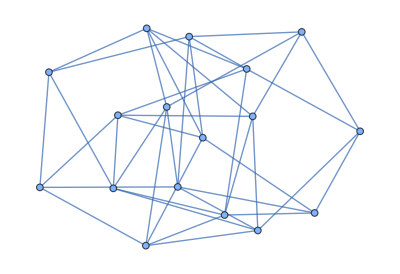
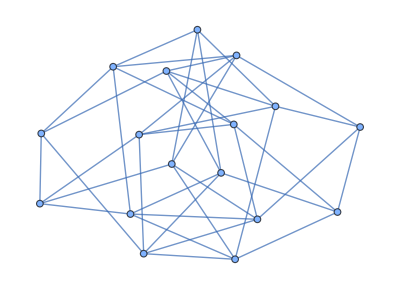
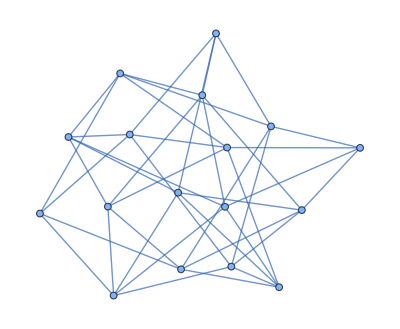
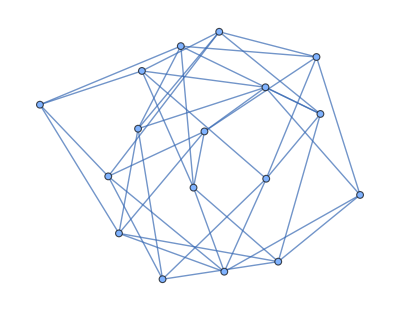
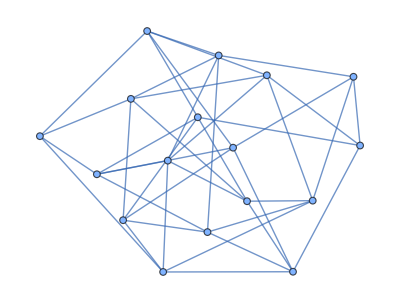
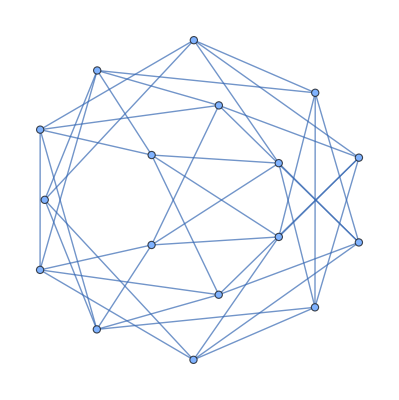
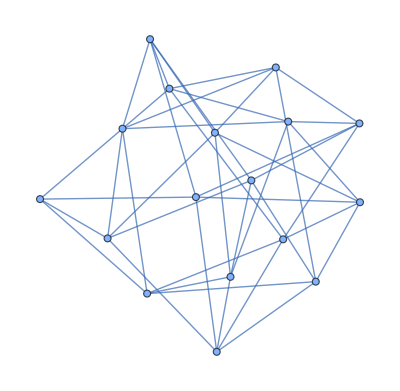

{{4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}}

False

```mathematica
gl=Import["https://a-boy.github.io/playmath/stage17-Ramsey-Numbers/r36_17.g6"];
gl={gl[[3]],gl[[5]],gl[[1]],gl[[2]],gl[[4]],gl[[6]],gl[[7]]}
VertexDegree/@gl
IsomorphicGraphQ[gl[[6]],gl[[7]]]
```

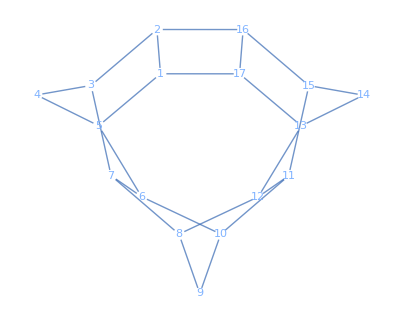
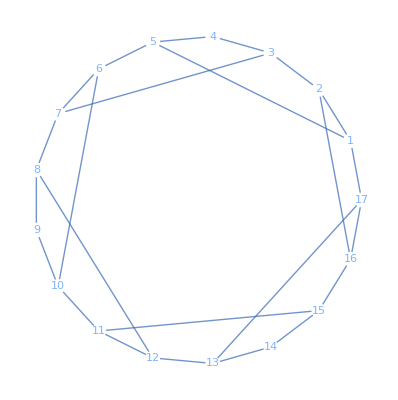

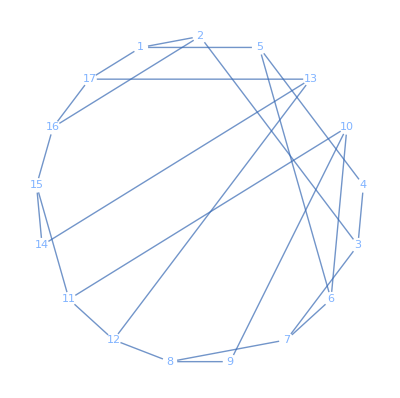
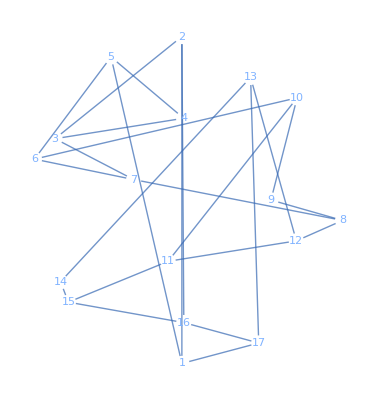
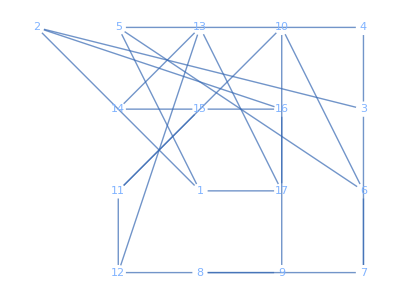
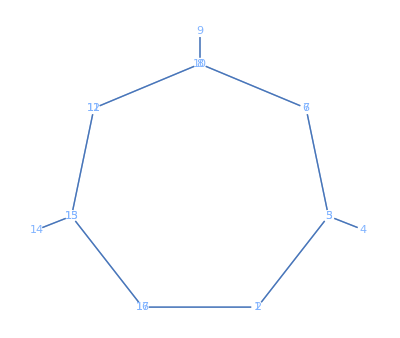
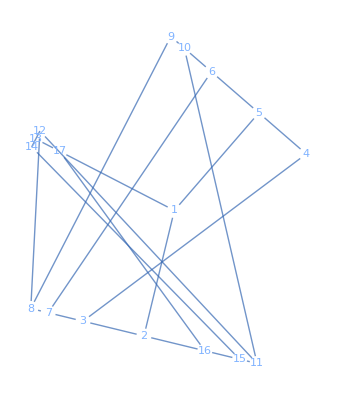
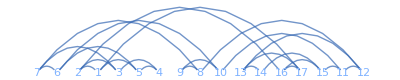

```mathematica
circleLayout[n_]:=Table[{Cos[2π/n i],Sin[2π/n i]},{i,n}];
papaya=AdjacencyGraph[{{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0}}];
{GraphPlot[papaya,VertexShapeFunction->"Name"],GraphPlot[papaya,VertexShapeFunction->"Name",VertexCoordinates->circleLayout[17]]}
Table[GraphPlot[papaya,VertexShapeFunction->"Name",GraphLayout->layout],{layout,{"CircularEmbedding","SpiralEmbedding","DiscreteSpiralEmbedding","HighDimensionalEmbedding","BalloonEmbedding","LinearEmbedding","StarEmbedding", "RadialEmbedding","SpectralEmbedding","SymmetricLayeredEmbedding"}}]
```

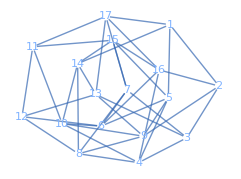
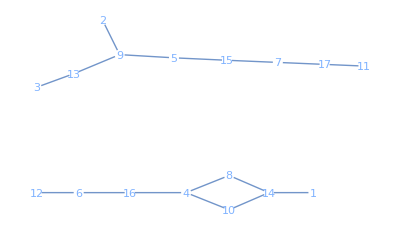
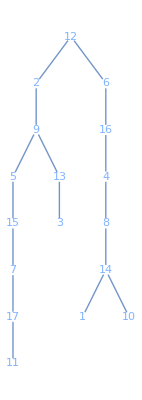
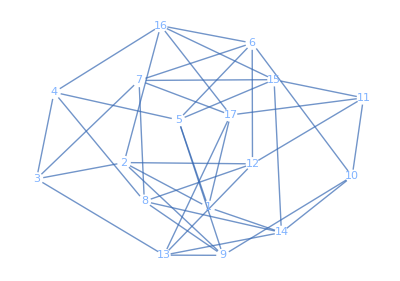
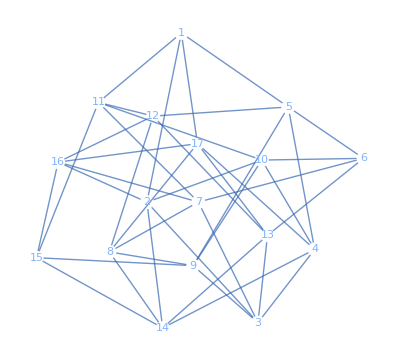
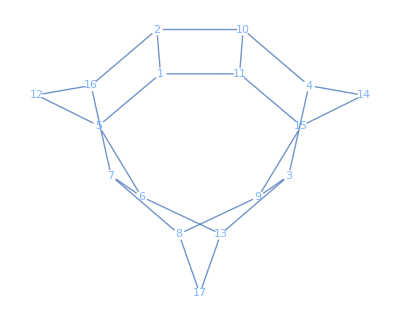
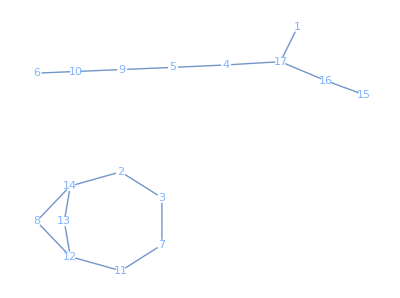
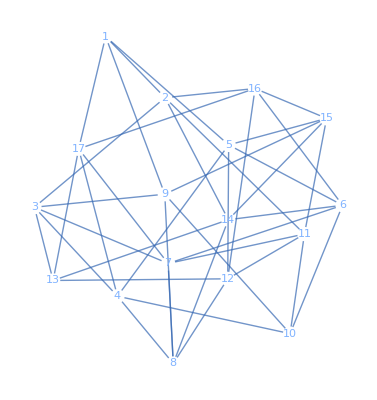
{-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-}

```mathematica
Table[
assoc=FindSubgraphIsomorphism[papaya,gl[[k]],1][[1]];
reverseAssoc=Association@KeyValueMap[#2->#1&,assoc];
g=Graph[EdgeList[gl[[k]]]/.reverseAssoc];
gl[[k]]=g;
sub=FindIsomorphicSubgraph[g,papaya,1][[1]];
GraphPlot[g,VertexShapeFunction->"Name",GraphLayout->"SpringElectricalEmbedding"]+GraphPlot[sub,VertexShapeFunction->"Name"]+
GraphPlot[body=GraphDifference[g,sub],VertexShapeFunction->"Name"],
{k,7}]
```

```mathematica
Export["E:\\cloud\\github\\a-boy\\playmath\\stage17-Ramsey-Numbers\\17-R36.g6",gl]
```

E:\cloud\github\a-boy\playmath\stage17-Ramsey-Numbers\17-R36.g6

```mathematica
MatrixForm@AdjacencyMatrix[g]
```

(0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
{1<->14,14<->10,10<->6,6<->7,7<->3,3<->2,2<->12,12<->13,13<->17,17<->16,16<->15,15<->11,11<->4,4<->8,8<->9,9<->5,5<->1}
```

{1<->14,14<->10,10<->6,6<->7,7<->3,3<->2,2<->12,12<->13,13<->17,17<->16,16<->15,15<->11,11<->4,4<->8,8<->9,9<->5,5<->1}

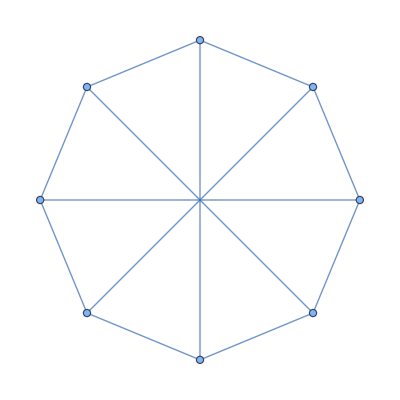

<|1→14,2→13,3→17,4→7,5→8,6→12,7→11,8→15|>

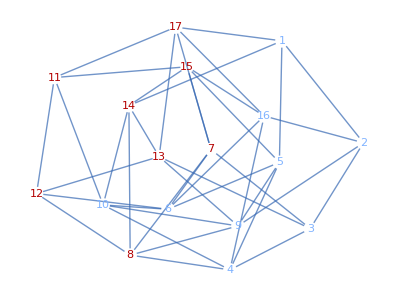

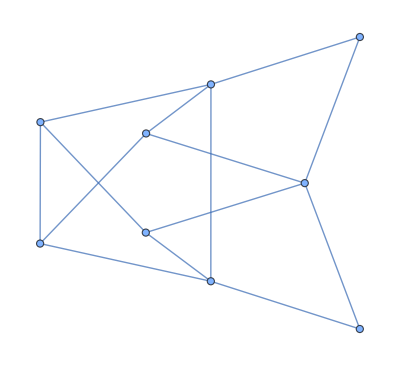

```mathematica
g8=CirculantGraph[8,{1,4}]

assoc=FindSubgraphIsomorphism[g8,gl[[1]],2][[1]]
GraphPlot[HighlightGraph[gl[[1]],Values@assoc],VertexShapeFunction->"Name"]
VertexDelete[gl[[1]],Values@assoc]
```

```mathematica
MatrixForm[m]
```

m

<|1→2,2→3,3→7,4→17,5→16,6→15,7→14,8→13,9→12,10→11,11→10,12→6,13→5,14→4,15→8,16→9|>

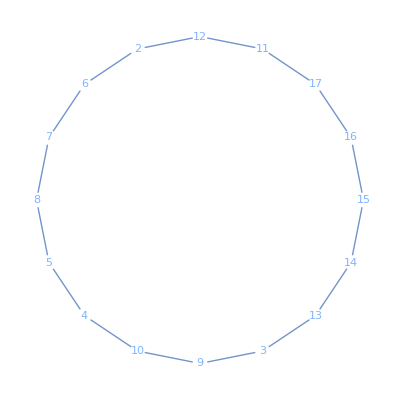

SparseArray[…]

(0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

SparseArray[…]

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

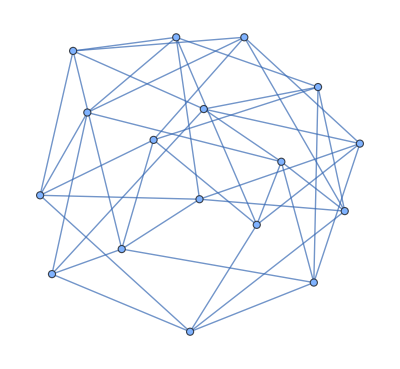

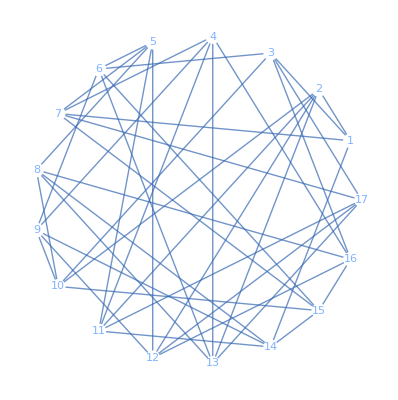

```mathematica
c16=CycleGraph[16];

assoc=FindSubgraphIsomorphism[c16,VertexDelete[gl[[6]],1],2][[1]]
(*reverseAssoc=Association@KeyValueMap[#2->#1&,assoc];
g=Graph[EdgeList[gl[[6]]]/.reverseAssoc]*)
FindIsomorphicSubgraph[g,c16,VertexShapeFunction->"Name"]
(*pm=PermutationMatrix[{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12}]
ipm=pm+(IdentityMatrix[Dimensions[pm][[1]]]-DiagonalMatrix[Diagonal[pm]])
MatrixForm@ipm
Det[ipm]
m=pm.AdjacencyMatrix[gl[[6]]].pm
MatrixForm[m]*)
m=AdjacencyMatrix[gl[[6]]]
MatrixForm[m]
pm=m[[{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12},{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12}]]
MatrixForm[pm]
g=AdjacencyGraph[pm]
GraphPlot[g,VertexShapeFunction->"Name",VertexCoordinates->circleLayout[17]]
```

```mathematica
Export["E:\\cloud\\github\\a-boy\\playmath\\stage17-Ramsey-Numbers\\17R36-1.graphml",gl[[1]]]
Export["E:\\cloud\\github\\a-boy\\playmath\\stage17-Ramsey-Numbers\\17R36-2.graphml",gl[[2]]]
```

E:\cloud\github\a-boy\playmath\stage17-Ramsey-Numbers\17R36-1.graphml

E:\cloud\github\a-boy\playmath\stage17-Ramsey-Numbers\17R36-2.graphml

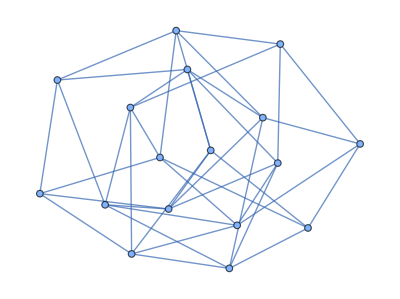

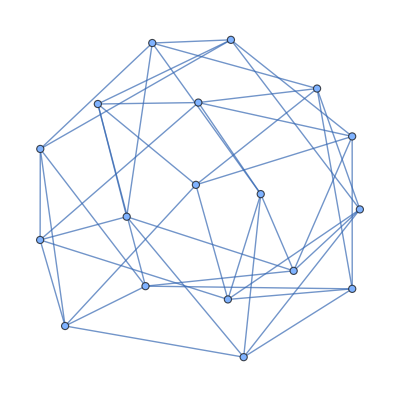

```mathematica
gl[[1]]
g=EdgeAdd[gl[[1]],{0<->1,0<->2,0<->3,0<->11,0<->12}]
```

```mathematica
Export["E:\\temp\\17R36-1-add-onenode.graphml",g]
```

E:\temp\17R36-1-add-onenode.graphml